```mathematica
(*Rules for Stern Judging*)
```

```mathematica
(* G -> B *)
Reduce[{g+ϵ-1+g-ϵ*g*(1-g)>0,1≥ g≥ 0,1≥ ϵ≥ 0}]
```

(0<g≤1/2&&(1-2 g)/(1-g+g^2)<ϵ≤1)||(1/2<g≤1&&0≤ϵ≤1)

```mathematica
(* B -> G *)
Reduce[{g+ϵ*g*(1-g)-1+g-ϵ>0,1≥ g≥ 0,1≥ ϵ≥ 0}]
```

1/2<g≤1&&0≤ϵ<(-1+2 g)/(1-g+g^2)

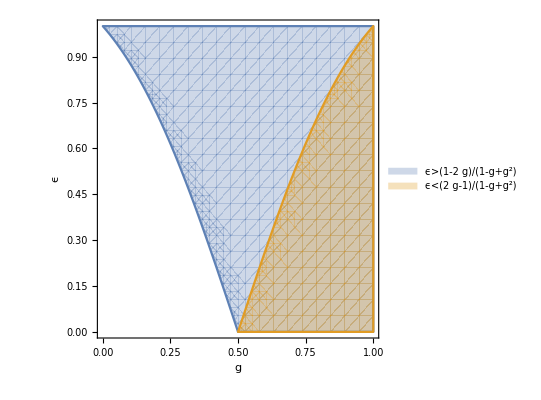

```mathematica
RegionPlot[{ϵ>(1-2 g)/(1-g+g^2),ϵ<(2 g-1)/(1-g+g^2)},{g,0,1},{ ϵ,0,1},PlotLegends->"Expressions",FrameLabel->Automatic]
```